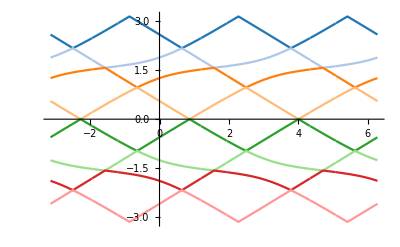

```mathematica
ClearAll["Global` "]
C0 = 1152 (-4 + c^2) (-1 + c^2 - Cos[2 d] + c^2 Cos[2 d]) + 864 c^2 Sin[2 d]^2;
C1 = Sqrt[-4 (160 - 128 c^2 + 4 c^4 + 96 Cos[2 d] - 96 c^2 Cos[2 d])^3 + (-16 (-4 + c^2)^3 - C0)^2];
C2 = (16 (-4 + c^2)^3 + C0 - C1)^(1/3);
C3 = (40 - 32 c^2 + c^4 + 24 Cos[2 d] - 24 c^2 Cos[2 d]) / (3 2^(2/3) C2) + C2/(24 2^(1/3));
C4 = Sqrt[(1/4) (4 - c^2) + (1/12) (-4 + c^2) + C3];
(*
  Use Re[] to take only the real part for each solution because, while the imaginary part
  should always be zero, the machine precision sometimes yields a small imaginary part.
*)
solns := {
{p ->-ArcCos[Re[-C4/2 -  Sqrt[(1/3) (4 - c^2) - C3 - (c Sin[2 d])/(2 C4)]/2]]},
{p ->-ArcCos[Re[-C4/2 +  Sqrt[(1/3) (4 - c^2) - C3 - (c Sin[2 d])/(2 C4)]/2]]},
{p ->-ArcCos[Re[ C4/2 -  Sqrt[(1/3) (4 - c^2) - C3 + (c Sin[2 d])/(2 C4)]/2]]},
{p ->-ArcCos[Re[ C4/2 +  Sqrt[(1/3) (4 - c^2) - C3 + (c Sin[2 d])/(2 C4)]/2]]},
{p ->ArcCos[Re[ C4/2 +  Sqrt[(1/3) (4 - c^2) - C3 + (c Sin[2 d])/(2 C4)]/2]]},
{p ->ArcCos[Re[ C4/2 -  Sqrt[(1/3) (4 - c^2) - C3 + (c Sin[2 d])/(2 C4)]/2]]},
{p ->ArcCos[Re[-C4/2 +  Sqrt[(1/3) (4 - c^2) - C3 - (c Sin[2 d])/(2 C4)]/2]]},
{p ->ArcCos[Re[-C4/2 -  Sqrt[(1/3) (4 - c^2) - C3 - (c Sin[2 d])/(2 C4)]/2]]}
}

psolns = p/.solns/.{c->0.85};
(* Plot from -Pi to 2 Pi to more clearly show the periodicity *)
Plot[{psolns[[8]], psolns[[7]], psolns[[6]], psolns[[5]],
	psolns[[4]], psolns[[3]], psolns[[2]], psolns[[1]]}, 
	{d, -Pi, 2Pi}, PlotStyle->
      {RGBColor["#1f77b4"],RGBColor["#aec7e8"],RGBColor["#ff7f0e"],RGBColor["#ffbb78"],
       RGBColor["#2ca02c"],RGBColor["#98df8a"],RGBColor["#d62728"],RGBColor["#ff9896"]}]
```